```mathematica
∫_0^(π/2) Sin[x]^n/(Sin[x]^n+Cos[x]^n)ⅆx
```

$Aborted

```mathematica
Integrate[Sin[x]^n/(Sin[x]^n+Cos[x]^n),{x,0,π/2},Assumptions->n∈]
```

$Aborted

```mathematica
Integrate[With[{n=1},Sin[x]^n/(Sin[x]^n+Cos[x]^n)],{x,0,π/2},Assumptions->n∈]
```

π/4

```mathematica
Table[Integrate[With[{n=a},Sin[x]^n/(Sin[x]^n+Cos[x]^n)],{x,0,π/2}],{a,1,10}]
```

$Aborted

```mathematica
Integrate[With[{n=2},Sin[x]^n/(Sin[x]^n+Cos[x]^n)],{x,0,π/2},Assumptions->n∈]
```

π/4

```mathematica
Integrate[With[{n=3},Sin[x]^n/(Sin[x]^n+Cos[x]^n)],{x,0,π/2},Assumptions->n∈]
```

π/4

```mathematica
Integrate[With[{n=4},Sin[x]^n/(Sin[x]^n+Cos[x]^n)],{x,0,π/2},Assumptions->n∈]
```

π/4

```mathematica
Table[Sin[x]^n/(Sin[x]^n+Cos[x]^n),{n,1,10}]
```

{Sin[x]/(Cos[x]+Sin[x]),Sin[x]^2/(Cos[x]^2+Sin[x]^2),Sin[x]^3/(Cos[x]^3+Sin[x]^3),Sin[x]^4/(Cos[x]^4+Sin[x]^4),Sin[x]^5/(Cos[x]^5+Sin[x]^5),Sin[x]^6/(Cos[x]^6+Sin[x]^6),Sin[x]^7/(Cos[x]^7+Sin[x]^7),Sin[x]^8/(Cos[x]^8+Sin[x]^8),Sin[x]^9/(Cos[x]^9+Sin[x]^9),Sin[x]^10/(Cos[x]^10+Sin[x]^10)}

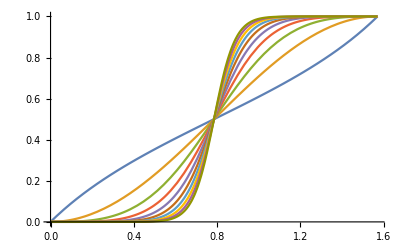

```mathematica
Plot[
{Sin[x]/(Cos[x]+Sin[x]),Sin[x]^2/(Cos[x]^2+Sin[x]^2),Sin[x]^3/(Cos[x]^3+Sin[x]^3),Sin[x]^4/(Cos[x]^4+Sin[x]^4),Sin[x]^5/(Cos[x]^5+Sin[x]^5),Sin[x]^6/(Cos[x]^6+Sin[x]^6),Sin[x]^7/(Cos[x]^7+Sin[x]^7),Sin[x]^8/(Cos[x]^8+Sin[x]^8),Sin[x]^9/(Cos[x]^9+Sin[x]^9),Sin[x]^10/(Cos[x]^10+Sin[x]^10)}
,{x,0,π/2}]
```

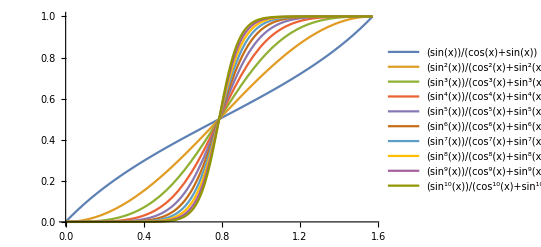

```mathematica
Plot[
{Sin[x]/(Cos[x]+Sin[x]),Sin[x]^2/(Cos[x]^2+Sin[x]^2),Sin[x]^3/(Cos[x]^3+Sin[x]^3),Sin[x]^4/(Cos[x]^4+Sin[x]^4),Sin[x]^5/(Cos[x]^5+Sin[x]^5),Sin[x]^6/(Cos[x]^6+Sin[x]^6),Sin[x]^7/(Cos[x]^7+Sin[x]^7),Sin[x]^8/(Cos[x]^8+Sin[x]^8),Sin[x]^9/(Cos[x]^9+Sin[x]^9),Sin[x]^10/(Cos[x]^10+Sin[x]^10)}
,{x,0,π/2},PlotLegends->"Expressions"]
```

```mathematica
Table[(Sin[x]/(Sin[x]+Cos[x]))^n,{n,1,10}]
```

{Sin[x]/(Cos[x]+Sin[x]),Sin[x]^2/(Cos[x]+Sin[x])^2,Sin[x]^3/(Cos[x]+Sin[x])^3,Sin[x]^4/(Cos[x]+Sin[x])^4,Sin[x]^5/(Cos[x]+Sin[x])^5,Sin[x]^6/(Cos[x]+Sin[x])^6,Sin[x]^7/(Cos[x]+Sin[x])^7,Sin[x]^8/(Cos[x]+Sin[x])^8,Sin[x]^9/(Cos[x]+Sin[x])^9,Sin[x]^10/(Cos[x]+Sin[x])^10}

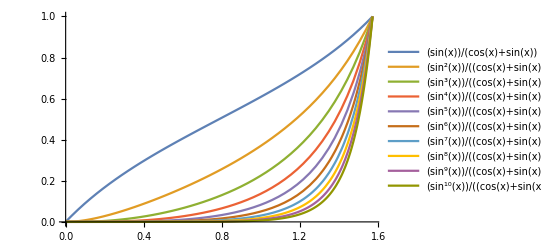

```mathematica
Plot[
{Sin[x]/(Cos[x]+Sin[x]),Sin[x]^2/(Cos[x]+Sin[x])^2,Sin[x]^3/(Cos[x]+Sin[x])^3,Sin[x]^4/(Cos[x]+Sin[x])^4,Sin[x]^5/(Cos[x]+Sin[x])^5,Sin[x]^6/(Cos[x]+Sin[x])^6,Sin[x]^7/(Cos[x]+Sin[x])^7,Sin[x]^8/(Cos[x]+Sin[x])^8,Sin[x]^9/(Cos[x]+Sin[x])^9,Sin[x]^10/(Cos[x]+Sin[x])^10}
,{x,0,π/2},PlotLegends->"Expressions"]
```

```mathematica
Table[x^i,{i,1,10}]
```

{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}

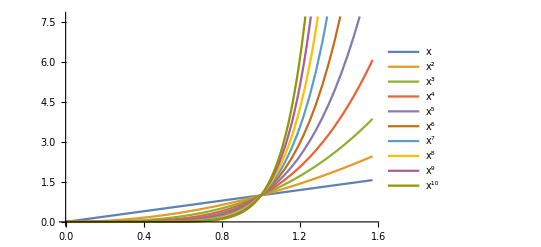

```mathematica
Plot[
{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}
,{x,0,π/2},PlotLegends->"Expressions"]
```

```mathematica
Integrate[{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},{x,0,1}]
```

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11}

```mathematica
Table[Integrate[f,{x,0,1}]==Integrate[f,{x,1,Subscript[a, f]}],{f,{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}}]
```

{1/2==-1/2+a_x^2/2,1/3==-1/3+(a_(x^2)^3)/3,1/4==-1/4+(a_(x^3)^4)/4,1/5==-1/5+(a_(x^4)^5)/5,1/6==-1/6+(a_(x^5)^6)/6,1/7==-1/7+(a_(x^6)^7)/7,1/8==-1/8+(a_(x^7)^8)/8,1/9==-1/9+(a_(x^8)^9)/9,1/10==-1/10+(a_(x^9)^10)/10,1/11==-1/11+(a_(x^10)^11)/11}

```mathematica
Table[Solve[Integrate[f,{x,0,1}]==Integrate[f,{x,1,Subscript[a, f]}],Subscript[a, f],PositiveReals],{f,{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}}]
```

{{{a_x→√2}},{{a_(x^2)→Root1.26Root[-2+#1^3&,1]1.2599210498948732}},{{a_(x^3)→Root1.19Root[-2+#1^4&,2]1.189207115002721}},{{a_(x^4)→Root1.15Root[-2+#1^5&,1]1.148698354997035}},{{a_(x^5)→Root1.12Root[-2+#1^6&,2]1.122462048309373}},{{a_(x^6)→Root1.10Root[-2+#1^7&,1]1.1040895136738123}},{{a_(x^7)→Root1.09Root[-2+#1^8&,2]1.0905077326652577}},{{a_(x^8)→Root1.08Root[-2+#1^9&,1]1.080059738892306}},{{a_(x^9)→Root1.07Root[-2+#1^10&,2]1.0717734625362931}},{{a_(x^10)→Root1.07Root[-2+#1^11&,1]1.0650410894399627}}}

```mathematica
Integrate[f'[x],x]
```

f[x]

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]
```

f[x] g[x]

```mathematica
Integrate[f'[g[x]]g'[x],x]
```

f[g[x]]

```mathematica
D[f[g[x]],{x,2}]
```

g'[x]^2 f''[g[x]]+f'[g[x]] g''[x]

```mathematica
Integrate[g'[x]^2 f''[g[x]]+f'[g[x]] g''[x],x]
```

f'[g[x]] g'[x]

```mathematica
-Cosh[t]Sinh[t]
```

-Cosh[t] Sinh[t]

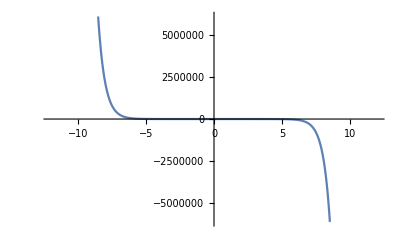

```mathematica
Plot[-Cosh[t] Sinh[t],{t,-12.,12.}]
```

```mathematica
Cosh[t]
```

Cosh[t]

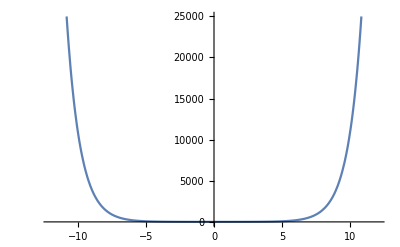

```mathematica
Plot[Cosh[t],{t,-12.,12.}]
```

```mathematica
Sinh[t]
```

Sinh[t]

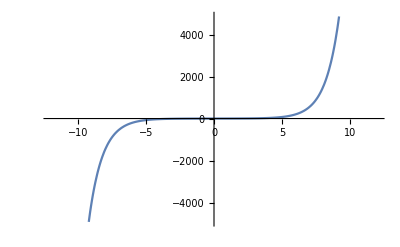

```mathematica
Plot[Sinh[t],{t,-12.,12.}]
```

```mathematica
Plot[-Cosh[t] Sinh[t],{t,-12.,12.}]
```

-Graphics-

```mathematica
LaplaceTransform[-Cosh[t] Sinh[t],t,s]
```

-1/(-4+s^2)

```mathematica
-1/(-4+s^2)
```

-1/(-4+s^2)

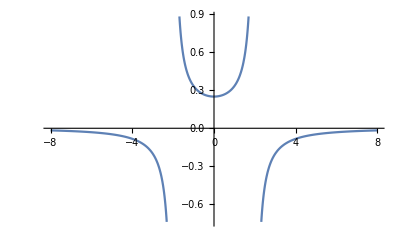

```mathematica
Plot[-1/(-4+s^2),{s,-8,8}]
```

```mathematica
Integrate[-1/(-4+s^2),{s,0,2/ⅈ}]
```

-(ⅈ π)/8

```mathematica
DMSList[N[-(ⅈ π)/(8 °)]]
```

DMSList::num: 0.-22.5 ⅈ cannot be interpreted as a numerical angle specification.

DMSList[0.-22.5 ⅈ]

```mathematica
π Rationalize[N[-(ⅈ π)/8]/π]
```

-(ⅈ π)/8

```mathematica
p^(1-a) q^a/.{p->{t,t},q->{Cos[t],Sin[t]}}
```

{t^(1-a) Cos[t]^a,t^(1-a) Sin[t]^a}

```mathematica
Manipulate[
ParametricPlot[
{t^(1-a) Cos[t]^a,t^(1-a) Sin[t]^a}
,{t,0,2π}]
,{a,0.001,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{t^(1-a) Cos[t]^a,t^(1-a) Sin[t]^a}
,{t,0,2π},PlotRange->{{-2π,2π},{-2π,2π}}]
,{a,0.001,1}]
```

Power::indet: Indeterminate expression 0.^0. encountered.

```mathematica
D[f[g[h[x]]],x]
```

f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
∫f'[g[h[x]]] g'[h[x]] h'[x]ⅆx
```

f[g[h[x]]]

```mathematica
∫f'[g[h[x]]] g'[h[x]] h'[x]ⅆx
```

f[g[h[x]]]

```mathematica
D[f[x]g[x]h[x],x]
```

g[x] h[x] f'[x]+f[x] h[x] g'[x]+f[x] g[x] h'[x]

```mathematica
∫(g[x] h[x] f'[x]+f[x] h[x] g'[x]+f[x] g[x] h'[x])ⅆx
```

f[x] g[x] h[x]

```mathematica
e==t+u
```

e==t+u

```mathematica
e==t+u
```

e==t+u

```mathematica
∫f'[g[h[x]]] g'[h[x]] h'[x]ⅆx
```

f[g[h[x]]]

```mathematica
∫f'[g[h[x]]] g'[h[x]]ⅆx
```

∫f'[g[h[x]]] g'[h[x]]ⅆx

```mathematica
∫f'[g[h[x]]] g'[h[x]]ⅆx
```

∫f'[g[h[x]]] g'[h[x]]ⅆx

```mathematica
f'[g[h[x]]] g'[h[x]]h'[x]==a h'[x]
```

f'[g[h[x]]] g'[h[x]] h'[x]==a h'[x]

```mathematica
Integrate[f'[g[h[x]]] g'[h[x]]h'[x],x]==Integrate[a h'[x],x]
```

f[g[h[x]]]==a h[x]

```mathematica
Integrate[f'[g[h[x]]] g'[h[x]]h'[x],x]==Integrate[a[x] h'[x],x]
```

f[g[h[x]]]==∫a[x] h'[x]ⅆx

```mathematica
f[z_]:=Gamma[z-I]^2/Gamma[z+I]^2
```

```mathematica
textureSphere=Texture[Rasterize[ComplexPlot[f[Cot[Im[w]] Exp[I Re[w]]],{w,-π,π+π/2 I},Sequence[ColorFunction->"CyclicLogAbsArg",Frame->False,PlotRangePadding->0,BoundaryStyle->None]],ImageResolution->400]];
```

```mathematica
sphere=SphericalPlot3D[Cos[ϕ],{ϕ,0,π/2},{θ,-π,π},TextureCoordinateFunction->({#5,#4}&),PlotStyle->Directive[textureSphere],Sequence[Mesh->{{0.5}},MeshFunctions->{#3&},MeshStyle->Directive[Thick,Black],PlotPoints->40,Lighting->"Neutral",ViewPoint->{-2,-2,1.5},BoundaryStyle->None]]
```

-Graphics3D-

```mathematica
texturePlane=Texture[Rasterize[ComplexPlot[f[z],{z,-(3/2)-(3 I)/2,3/2+(3 I)/2},Sequence[ColorFunction->"CyclicLogAbsArg",Epilog->{Thick,Circle[]},Frame->False,PlotRangePadding->0,BoundaryStyle->None]],ImageResolution->400]];
```

```mathematica
plane=Graphics3D[{texturePlane,Polygon[Sequence[{{(-3)/2,(-3)/2,0},{3/2,(-3)/2,0},{3/2,3/2,0},{(-3)/2,3/2,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]]},Sequence[ViewPoint->{-2,-2,1.5},Axes->True]];
```

```mathematica
Show[sphere,plane,BoxRatios->Automatic,PlotRange->{{-3/2,3/2},{-3/2,3/2},{0,1}}]
```

-Graphics3D-

```mathematica
AbsArgPlot[x^(1/3),{x,-3,3},PlotLegends->Automatic]
```

-Graphics-

```mathematica
CurveBySpherCurvature[kappatilde_,{s_,s0_,s1_},pnt00_,tan00_] :=Module[
{sol,x1,x2,l1,l2,l3,t1,t2,t3,n1,n2,n3},
{
sol=NDSolve[
{l1'[ss]==t1[ss],
l2'[ss]==t2[ss],
l3'[ss]==t3[ss],
t1'[ss]==-l1[ss]+kappatilde[ss]*n1[ss],
t2'[ss]==-l2[ss]+kappatilde[ss]*n2[ss],
t3'[ss]==-l3[ss]+kappatilde[ss]*n3[ss],
n1'[ss]==-kappatilde[ss]*t1[ss],
n2'[ss]==-kappatilde[ss]*t2[ss],
n3'[ss]==-kappatilde[ss]*t3[ss],
l1[s0]==pnt00[[1]],l2[s0]==pnt00[[2]],l3[s0]==pnt00[[3]],
t1[s0]==tan00[[1]],t2[s0]==tan00[[2]],t3[s0]==tan00[[3]],
n1[s0]==Cross[pnt00,tan00][[1]],
n2[s0]==Cross[pnt00,tan00][[2]],
n3[s0]==Cross[pnt00,tan00][[3]]},
{l1,l2,l3,t1,t2,t3,n1,n2,n3},
{ss,s0,s1}];
{l1[s],l2[s],l3[s]}/.sol[[1]]}[[1]]]
```

```mathematica
sphere:=ParametricPlot3D[{Cos[v],Cos[u]Sin[v],Sin[u]Sin[v]},{u,0,2π},{v,0,2π},Boxed->False,Axes->None,PlotStyle->None,MeshStyle->GrayLevel[0.85],Mesh->10,ImageSize->{250,250}]
```

```mathematica
func1[s_]=Cos[s];
func2[s_]=s;
func3[s_]=E^(0.1s)-1;
func4[s_]=0.9805806756909201 Cot[0.19611613513818404 s];
f={func1,func2,func3,func4};
cht[t_]=Table[CurveBySpherCurvature[f[[i]],{t,$MachineEpsilon,4Pi},{-1,0,0},{0,0,1}],{i,4}];
```

```mathematica
ch[s_]:=cht[s]
```

```mathematica
Manipulate[
Module[{φ, ψ},
φ=p[[1]];
ψ=p[[2]];
Grid[{{
ParametricPlot[{-(Y Cos[α]^2-2 Z Cos[α] Cos[ψ] Sin[α]+X Sin[2 α] Sin[φ] Sin[ψ]+Sin[α]^2 (-Y Cos[ψ]^2+(Y Cos[2 φ]+Z Sin[2 φ]) Sin[ψ]^2+X Cos[φ] Sin[2 ψ]))/(-1+X Cos[α]^2+Sin[2 α] (Z Cos[φ]-Y Sin[φ]) Sin[ψ]+Sin[α]^2 (X Cos[2 ψ]+(Y Cos[φ]+Z Sin[φ]) Sin[2 ψ])),-(Z Cos[α]^2-Z Cos[ψ]^2 Sin[α]^2+Y Cos[ψ] Sin[2 α]-2 X Cos[α] Cos[φ] Sin[α] Sin[ψ]+Sin[α]^2 ((-Z Cos[2 φ]+Y Sin[2 φ]) Sin[ψ]^2+X Sin[φ] Sin[2 ψ]))/(-1+X Cos[α]^2+Sin[2 α] (Z Cos[φ]-Y Sin[φ]) Sin[ψ]+Sin[α]^2 (X Cos[2 ψ]+(Y Cos[φ]+Z Sin[φ]) Sin[2 ψ]))}/.{X->ch[s][[j,1]],Y->ch[s][[j,2]],Z->ch[s][[j,3]]},{s,$MachineEpsilon,4π},PlotStyle->Darker@Green,AxesLabel->{y,z},PlotRange->If[pr,All,Switch[j,1,15,2,1,3,6,4,1]],ImageSize->1.25{250,200}],
Show[ParametricPlot3D[{X Cos[α]^2+Sin[2 α] (Z Cos[φ]-Y Sin[φ]) Sin[ψ]+Sin[α]^2 (X Cos[2 ψ]+(Y Cos[φ]+Z Sin[φ]) Sin[2 ψ]),Y Cos[α]^2-2 Z Cos[α] Cos[ψ] Sin[α]+X Sin[2 α] Sin[φ] Sin[ψ]+Sin[α]^2 (-Y Cos[ψ]^2+(Y Cos[2 φ]+Z Sin[2 φ]) Sin[ψ]^2+X Cos[φ] Sin[2 ψ]),Z Cos[α]^2-Z Cos[ψ]^2 Sin[α]^2+Y Cos[ψ] Sin[2 α]-2 X Cos[α] Cos[φ] Sin[α] Sin[ψ]+Sin[α]^2 ((-Z Cos[2 φ]+Y Sin[2 φ]) Sin[ψ]^2+X Sin[φ] Sin[2 ψ])}/.{X->ch[s][[j,1]],Y->ch[s][[j,2]],Z->ch[s][[j,3]]},{s,$MachineEpsilon,4π},PlotStyle->Red,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesOrigin->{0,0,0},Boxed->False,Axes->None],
Graphics3D[{{
{Opacity[.2],Sphere[]},
Text[Style["P",Blue,14],{1.3,0,0}]},
Sphere[{1,0,0},.07],
Sphere[{Cos[ψ],Cos[φ]Sin[ψ],Sin[φ]Sin[ψ]},.03],
Sphere[{-Cos[ψ],-Cos[φ]Sin[ψ],-Sin[φ]Sin[ψ]},.03],Line[{{Cos[ψ],Cos[φ]Sin[ψ],Sin[φ]Sin[ψ]},{-Cos[ψ],-Cos[φ]Sin[ψ],-Sin[φ]Sin[ψ]}}]}
],

ImageSize->1.25{220,220},SphericalRegion-> True,ViewPoint->{Left,Back}]
}}]],
Grid[{{
Control@{{j,1,Style["f(σ) =",12]},{1->"cos(σ)", 2->"σ",3->"e^(b σ) - 1, b = 0.1",4->"1 / √(1 + SuperscriptBox[b, 2]) cot( b σ/ √(1 + SuperscriptBox[b, 2]) ), b = 0.2"} ,PopupMenu },
Row[{Spacer[20],Control@{{p,{0,0},Style["(φ, ψ)",12]},{-π,-π/2},{π,π/2},{π/18,π/18}}  }],
Row[{Spacer[20],Control@{{pr,False,"variable plot range"},{False,True}}   }],
Spacer[{30,30}]
},
{
Control@{{α,0,Style["rotate by α",12]},0,2 3.14,.01,ImageSize->Medium,Appearance->"Labeled"},Text[Style[Row[{"(φ, ψ) = ",Dynamic[p]}],12]], Spacer[{30,30}]}}],
ControlPlacement->Top,
SaveDefinitions->True,
TrackedSymbols:> {j, p, α}]
```

```mathematica
Manipulate[
Module[{fx=#&,umin=-50,umax=50,du=.2,chartsize=3,xdomain,ydomain,functiondomain,myrange, t, sols,plane,xaxis,yaxis,du2,func,posy,posx,negx,negy,equator,m1,m2,zerosphere,infsphere,line,x1,x2,k,xk,tAc,g1,g2,g3},

ydomain=IntervalIntersection[Interval[{umin,umax}],toInterval[mydomain[fy]]][[1]];
If[MemberQ[ydomain,Null]||MemberQ[ydomain,True],ydomain={umin,umax}];
If[Length[ydomain]==1,ydomain=ydomain[[1]]];

xdomain=IntervalIntersection[Interval[{umin,umax}],toInterval[mydomain[fx]]][[1]];
If[MemberQ[xdomain,Null]||MemberQ[xdomain,True],xdomain={umin,umax}];
If[Length[xdomain]==1,xdomain=xdomain[[1]]];
functiondomain=IntervalIntersection[Interval[xdomain],Interval[ydomain]][[1]];

myrange={-chartsize,chartsize};
t=Quiet[NSolve[fy[x]==chartsize||fy[x]==-chartsize,x]];
tAc={};
If[t[[0]]==List,
For[k=1,k<=Length[t],k++,
xk=x/.t[[k]];
tAc=Append[tAc,xk]
]
];
tAc=Cases[tAc,_Real];
tAc=Sort[tAc];
If[Length[tAc]==0,
myrange={-chartsize,chartsize};,
If[Length[tAc]==2,
myrange=tAc;,
If[Length[tAc]==1,
If[fy[tAc[[1]]]==3,myrange={-chartsize,tAc[[1]]},
myrange={tAc[[1]],chartsize}
]
]
]
];
myrange=IntervalIntersection[Interval[{myrange[[1]],myrange[[2]]}],Interval[{-chartsize,chartsize}]][[1]];
myrange=IntervalIntersection[Interval[{myrange[[1]],myrange[[2]]}],Interval[functiondomain]][[1]];

plane={Thickness[.005],Opacity[.3],Hue[.5],First[ParametricPlot3D[{1.1,s,t},{t,-chartsize,chartsize},{s,-chartsize,chartsize}]]};
xaxis={Thickness[.005],Black,First[ParametricPlot3D[{1,t,0},{t,-chartsize,chartsize}]]};
yaxis={Thickness[.005],Black,First[ParametricPlot3D[{1,0,t},{t,-chartsize,chartsize}]]};
du2=.1(functiondomain[[2]]-functiondomain[[1]]);
posy=Text[TraditionalForm[f[x]],{1,0,chartsize+.4}];
posx=Text[TraditionalForm[x],{1,-chartsize-.4,0}];
equator={Thickness[.003],Blue,Opacity[.7],First[ParametricPlot3D[{Cos[p],Sin[p],0},{p,0,2*Pi},PlotPoints->100]]};
m1={Thickness[.003],Blue,Opacity[.7],First[ParametricPlot3D[{Cos[p],0,Sin[p]},{p,0,2*Pi},PlotPoints->100]]};
m2={Thickness[.003],Blue,Opacity[.7],First[ParametricPlot3D[{0,Cos[p],Sin[p]},{p,0,2*Pi},PlotPoints->100]]};
zerosphere={Blue,Sphere[{1,0,0},.05]};
infsphere={Red,Sphere[{-1,0,0},.05]};
line={Thickness[.004],Yellow,Line[{{-1,0,0},{1,-fx[((myrange[[2]]-myrange[[1]])/6)*param+(3*myrange[[1]]+3*myrange[[2]])/(6)],fy[((myrange[[2]]-myrange[[1]])/6)*param+(3*myrange[[1]]+3*myrange[[2]])/(6)]}}]};

g1=Graphics3D@{sphere[.8],equator,m1,m2,zerosphere,infsphere,Hue[0.9],Thickness[.003],Line[Table[projection2[{-1*fx[u],fy[u]}],{u,functiondomain[[1]]+.0001,functiondomain[[2]]-.0001,du/10}]]};
g3=Graphics3D@{xaxis,line,posx,posy,yaxis,plane};
g2=(* curve on sphere *) Graphics3D[{Thickness[.004],Red,First[ParametricPlot3D[{1,-fx[u/du2],fy[u/du2]},{u,functiondomain[[1]]+.001,functiondomain[[2]]-.001}]]}];
Show[If[spheremode,g1,{g1,g2,g3}],Boxed->False,SphericalRegion->True, ViewAngle-> Pi/10, ImageSize->{460,460}, ViewPoint-> {-4,0,0},PlotRange->{{-chartsize,chartsize},{-chartsize,chartsize},{-chartsize,chartsize}}]
],
"projection line",
 {{param,-3,""},-3,3, ImageSize-> Tiny} ,
Row[{Control[{{spheremode,False,"sphere only"},{True,False}} ]}],
Delimiter,
{{fy,Sin[#]&,TraditionalForm[f[x]==""]},{
#&->TraditionalForm[x],
1/#&->TraditionalForm[1/x],
#^2&->TraditionalForm[x^2],
1/#^2&->TraditionalForm[1/x^2],
#^(1/2)&->TraditionalForm[√x],
#^3&->TraditionalForm[x^3],
1/#^3&->TraditionalForm[1/x^3],
Sin[#]&->TraditionalForm[Sin[x]],
E^#&->TraditionalForm[e^x],
#*Cos[#]&->TraditionalForm[x Cos[x]],
Cosh[#]&->TraditionalForm[Cosh[x]],
E^Sin[#]&->TraditionalForm[e^Sin[x]],
ArcTan[#]&->TraditionalForm[ArcTan[x]],
Log[#]&->TraditionalForm[Log[x]],
Sin[#^2]&->TraditionalForm[Sin[x^2]]
}},
ControlPlacement-> Left,
Initialization :> (
mydomain[f_]:=Quiet[Reduce[Positive[f[x]]||Negative[f[x]]||f[x]==0,x,Reals]];
toInterval[routput_]:=Module[{lst},
lst=routput;
If[lst[[0]]===Or,lst=(lst/.Or->List),lst={lst}];
Interval@@Map[
If[#===True,{-Infinity,Infinity},
If[#[[0]]===Less||#[[0]]===LessEqual,{-Infinity,#[[2]]},
If[#[[0]]===Greater||#[[0]]===GreaterEqual,{#[[2]],Infinity},
If[#[[0]]===Equal,{#[[2]],#[[2]]},
If[#[[0]]===Inequality,{#[[1]],#[[-1]]}]]]]]&,
lst
]
];
sphere[n_]:={Green,Opacity[n],Sphere[{0,0,0},1]};
projection2[{x_,y_}]:={(4-x^2-y^2)/(x^2+y^2+4),(4x)/(x^2+y^2+4),(4y)/(x^2+y^2+4)};
)
]
```

```mathematica
(* Initialization code *)
sphere[s_,t_]={Sqrt[1-(s-1)^2] Cos[t],Sqrt[1-(s-1)^2]Sin[t],s};
complexplane[x_,y_]={x,y,-0.001};

complexplaneplot=ParametricPlot3D[complexplane[x,y],{x,-15,15},{y,-15,15},PlotStyle->{LightGray},Mesh->29,MeshStyle->LightRed];

sphereplot=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[z]]];
sphereplotnomesh=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[z]],Mesh->False];
sphereplotopacity=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle->Opacity[.5]];
sphereplotopacitynomesh=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle->Opacity[.5],Mesh->False];

yellowsphereplot=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[.1]]];
yellowsphereplotopacity=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[.1]],PlotStyle->Opacity[.5]];
yellowsphereplotnomesh=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[.1]],Mesh->False];
yellowsphereplotopacitynomesh=ParametricPlot3D[sphere[s,t],{t,0,2Pi},{s,0,2},ColorFunction->Function[{x,y,z},Hue[.1]],PlotStyle->Opacity[.5],Mesh->False];

(* For any given {s,t} pair, projectionline[u,s,t] is a line P + u V that connects {0,0,2} to the sphere at the point sphere[s,t] *)
projectionline[u_,s_,t_]=Simplify[{0,0,2}+u (sphere[s,t]-{0,0,2})];

(* Next find when the z-component of tangentline[u,s,t] is 0 in terms of u *)
Solve[projectionline[u,s,t][[3]]==0,u];

(* Plug u->1/(1-s) into projectionline[u,s,t] to find the point on z = 0 associated with its corresponding point on the sphere, sphere[s,t] *)
projectionline[-2/(-2+s),s,t];

(* Finally, rescale the lines so that any particular line starts at sphere[s,t] and moves to z = 0 as a new parameter, v, varies from 0 to 1. *)
surface[v_,s_,t_]=Simplify[sphere[s,t]+v (projectionline[-2/(-2+s),s,t]-sphere[s,t])];

(* Next, we will map some parametric curves (f(t),g(t)) between the complex plane and the Riemann sphere using the following techniques;
For the line: Solve[Simplify[surface[1,s,t]]=={w,w-3,0},{s,t}];
For the circle: Solve[Simplify[surface[1,s,t]]=={Cos[w]+2,Sin[w],0},{s,t}];
For the parabola: Solve[Simplify[surface[1,s,t]]=={w^2+1,w,0},{s,t}];
For the hyperbola: Solve[Simplify[surface[1,s,t]]=={Tan[w],Sec[w],0},{s,t}]; *)
riemannline1[u_,w_]=surface[u,(2 (9-6 w+2 w^2))/(13-6 w+2 w^2),-ArcCos[-w/(√(9-6 w+2 w^2))]];
riemannline2[u_,w_]=surface[u,(2 (9-6 w+2 w^2))/(13-6 w+2 w^2),ArcCos[-w/(√(9-6 w+2 w^2))]];
riemanncircle1[u_,w_]=surface[u,(2 (5+4 Cos[w]))/(9+4 Cos[w]),-ArcCos[-(2+Cos[w])/(√(4+4 Cos[w]+Cos[w]^2+Sin[w]^2))]];
riemanncircle2[u_,w_]=surface[u,(2 (5+4 Cos[w]))/(9+4 Cos[w]),ArcCos[-(2+Cos[w])/(√(4+4 Cos[w]+Cos[w]^2+Sin[w]^2))]];
riemannparabola1[u_,w_]=surface[u,(2 (1+3 w^2+w^4))/(5+3 w^2+w^4),-ArcCos[-(1+w^2)/(√(1+3 w^2+w^4))]];
riemannparabola2[u_,w_]=surface[u,(2 (1+3 w^2+w^4))/(5+3 w^2+w^4),ArcCos[-(1+w^2)/(√(1+3 w^2+w^4))]];
riemannhyperbola1[u_,w_]=surface[u,-(2 (-3+Cos[2 w]))/(7+3 Cos[2 w]),-ArcCos[-Tan[w]/(√(Sec[w]^2+Tan[w]^2))]];
riemannhyperbola2[u_,w_]=surface[u,-(2 (-3+Cos[2 w]))/(7+3 Cos[2 w]),ArcCos[Tan[w]/(√(Sec[w]^2+Tan[w]^2))]];
```

```mathematica
Manipulate[

Show[
Which[showcurve=="none",
Graphics3D[Point[{0,0,0}]],
showcurve=="line",
Show[ParametricPlot3D[riemannline1[1,w],{w,3,30},PlotStyle->{Red,Thickness[curvethickness]}],
ParametricPlot3D[riemannline2[1,w],{w,-30,3},PlotStyle->{Red,Thickness[curvethickness]}],ParametricPlot3D[riemannline1[0,w],{w,3,30},PlotStyle->{Red,Thickness[curvethickness]}],
ParametricPlot3D[riemannline2[0,w],{w,-30,3},PlotStyle->{Red,Thickness[curvethickness]}],
ParametricPlot3D[riemannline1[v,w],{w,3,30},PlotStyle->{Red,Thickness[curvethickness]}],
ParametricPlot3D[riemannline2[v,w],{w,-30,3},PlotStyle->{Red,Thickness[curvethickness]}],
If[showcurvelines==False,Graphics3D[Point[{0,0,0}]],Join[Table[Graphics3D[Line[{{0,0,2},riemannline2[v,j]}]],{j,-30,3,0.5}],Table[Graphics3D[Line[{{0,0,2},riemannline1[v,j]}]],{j,3,30,0.5}]]]
],
showcurve=="circle",
Show[ParametricPlot3D[{riemanncircle1[1,w],riemanncircle2[1,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],ParametricPlot3D[{riemanncircle1[0,w],riemanncircle2[0,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],ParametricPlot3D[{riemanncircle1[v,w],riemanncircle2[v,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],
If[showcurvelines==False,Graphics3D[Point[{0,0,0}]],Join[Table[Graphics3D[Line[{{0,0,2},riemanncircle1[v,j]}]],{j,0,30,1}],Table[Graphics3D[Line[{{0,0,2},riemanncircle2[v,j]}]],{j,0,30,1}]]]
],
showcurve=="parabola",
Show[ParametricPlot3D[{riemannparabola1[1,w],riemannparabola2[1,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],ParametricPlot3D[{riemannparabola1[0,w],riemannparabola2[0,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],ParametricPlot3D[{riemannparabola1[v,w],riemannparabola2[v,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],
If[showcurvelines==False,Graphics3D[Point[{0,0,0}]],Join[Table[Graphics3D[Line[{{0,0,2},riemannparabola1[v,j]}]],{j,0,30,1}],Table[Graphics3D[Line[{{0,0,2},riemannparabola2[v,j]}]],{j,0,30,1}]]]
],
showcurve=="hyperbola",
Show[ParametricPlot3D[{riemannhyperbola1[1,w],riemannhyperbola2[1,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],ParametricPlot3D[{riemannhyperbola1[0,w],riemannhyperbola2[0,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],ParametricPlot3D[{riemannhyperbola1[v,w],riemannhyperbola2[v,w]},{w,0,30},PlotStyle->{{Red,Thickness[curvethickness]},{Red,Thickness[curvethickness]}}],
If[showcurvelines==False,Graphics3D[Point[{0,0,0}]],Join[Table[Graphics3D[Line[{{0,0,2},riemannhyperbola1[v,j]}]],{j,0,30,1}],Table[Graphics3D[Line[{{0,0,2},riemannhyperbola2[v,j]}]],{j,0,30,1}]]]]
],

If[showpoints==True,Table[Graphics3D[{If[showpointcolor==True,Hue[s/2],Black],PointSize[pointsize],Point[surface[v,s,t]]}],{t,0,2 Pi,tjumppoints},{s,0.0001,1.9999,sjumppoints}],Graphics3D[Point[{0,0,0}]]],

If[showlines==True,Table[Graphics3D[{If[showcolor==True,Hue[s/2],Black],Thickness[linethickness],Line[{{0,0,2},surface[v,s,t]}]}],{t,0,2 Pi,tjumplines},{s,0.00001,1.9999,sjumplines}],Graphics3D[Point[{0,0,0}]]],

If[showaxes==True,Graphics3D[{Thickness[.008],Style[Text["Infinity",{0,0,2.5-zoom/10}],16],Style[Text["Im",{0,3/zoom,.3}],{12,Bold}],Style[Text["Re",{3/zoom,0,.3}],{12,Bold}],InfiniteLine[{0,0,0},{1,0,0}],InfiniteLine[{0,0,0},{0,1,0}]}],Graphics3D[Point[{0,0,0}]]],

If[showcomplexplane==True,complexplaneplot,Graphics3D[Point[{0,0,0}]]],

Which[showsphere==True&&showmesh==True&&opacity==False&&colorsphere==True,
sphereplot,
showsphere==True&&showmesh==False&&opacity==False&&colorsphere==True, 
sphereplotnomesh,
showsphere==True&&showmesh==True&&opacity==True&&colorsphere==True,
sphereplotopacity,
showsphere==True&&showmesh==False&&opacity==True&&colorsphere==True,
sphereplotopacitynomesh,
showsphere==True&&showmesh==True&&opacity==False&&colorsphere==False, 
yellowsphereplot,
showsphere==True&&showmesh==False&&opacity==False&&colorsphere==False, 
yellowsphereplotnomesh,
showsphere==True&&showmesh==True&&opacity==True&&colorsphere==False, 
yellowsphereplotopacity,
showsphere==True&&showmesh==False&&opacity==True&&colorsphere==False, 
yellowsphereplotopacitynomesh,
showsphere==False,
Graphics3D[Point[{0,0,0}]]],

If[showsurface==True,ParametricPlot3D[surface[v,s,t],{s,0.00001,1.99},{t,0,2 Pi},ColorFunction->Function[{x,y,z},If[colorsphere==True,Hue[z],Hue[.1]]],PlotStyle->Opacity[If[opacity==False,1,.5]],Mesh->If[showmesh==True,True,False]],Graphics3D[Point[{0,0,0}]]],

PlotRange->{{-3/zoom,3/zoom},{-3/zoom,3/zoom},{-0.2,2}},
ImageSize->{360,400},
SphericalRegion->False,
Background->LightYellow,
ViewPoint->{5,-5,4},
Boxed->False,
Axes->False
],

Control[{{v,0,"unwrap sphere"},0,0.99,ImageSize->490,ControlType->Animator, AnimationRunning->False,ControlPlacement->Top}],
Delimiter,
Column[{Row[{Control[{{showcomplexplane,True,"complex plane  "},{True,False}}],Control[{{showaxes,True,"   axes/labels         "},{True,False}}]}],
Row[{Control[{{showsurface,True,"surface              "},{True,False}}],Control[{{showsphere,True,"   Riemann sphere"},{True,False}}]}],
Row[{Control[{{colorsphere,True,"rainbow colors "},{True,False}}],Control[{{showmesh,True,"   mesh                  "},{True,False}}]}],
Row[{Control[{{zoom,4/3,"zoom"},7/3,1/3,ImageSize->Tiny}],Control[{{opacity,False,"   translucent  "},{True,False}}]}]
}],
Delimiter,Column[{Row[{Control[{{showcurve,"none","show curve"},{"none","line","circle","parabola","hyperbola"},ControlType->PopupMenu,ImageSize->{79,20}}]}],
Row[{Control[{{curvethickness,0.008,"curve thickness"},.008,.03,ImageSize->Tiny}]}],
Row[{Control[{{showcurvelines,False,"projection lines on curve"},{True,False}}]}]
}],
Delimiter,Column[{Row[{Control[{{showpoints,False,"sample points on sphere "},{True,False}}]}],
Row[{Control[{{showpointcolor,False,"rainbow colors on points"},{True,False}}]}],
Row[{Control[{{pointsize,0.015,"point size            "},.01,.03,ImageSize->Tiny}]}],Row[{Control[{{tjumppoints,Pi/8,"point count (Δθ)"},{Pi/16,Pi/8,Pi/6,Pi/4,Pi/2},ControlType->Manipulator,ImageSize->Tiny}]}],Row[{Control[{{sjumppoints,.25,"point count (Δh)"},{.015,.05,.1,.25,.5,1},ControlType->Manipulator,ImageSize->Tiny}]}]}],
Delimiter,
Column[{Row[{Control[{{showlines,False,"stereographic projection lines"},{True,False}}]}],
Row[{Control[{{showcolor,False,"rainbow colors on lines           "},{True,False}}]}],
Row[{Control[{{linethickness,0.001,"line thickness   "},.001,.008,ImageSize->Tiny}]}],Row[{Control[{{tjumplines,Pi/8,"line count (Δθ)"},{Pi/32,Pi/16,Pi/8,Pi/4,Pi/2},ControlType->Manipulator,ImageSize->Tiny}]}],Row[{Control[{{sjumplines,.5,"line count (Δh)"},{.015,.05,.1,.25,.5,1},ControlType->Manipulator,ImageSize->Tiny}]}]}],
ControlPlacement->Left,
SaveDefinitions->True]
```

```mathematica
(*********** preliminary ***********)

imageSize=300;
labelStyle=Directive[FontFamily->"Helvetica",FontSize->11];
mesh={10,10};
meshStyle=Directive[Thickness[.005],Black];
boundaryStyle=Directive[Black,Thickness[.005]];
spacings={0,0.};
```

```mathematica
min=10.^-11;
```

```mathematica
frameLabelζ={{"η",None},{"ξ","Cell["ζ",ExpressionUUID->"8c2c9bcc-f58f-4824-a1ca-6a7dabb69927"] plane"}};
```

```mathematica
frameLabelz={{Style["y",Italic],None},{Style["x",Italic],Row[{Style["z",Italic]," plane"}]}};
```

```mathematica
plotStyleζ=Directive[Lighter[RGBColor[.775,.225,0],.8],Specularity[RGBColor[.775,.225,0],1],Opacity[.5],Glow[RGBColor[.775,.225,0]]];
```

```mathematica
plotStylez=Directive[Lighter[RGBColor[0,.167,.833],.8],Specularity[RGBColor[0,.167,.833],1],Opacity[.5],Glow[RGBColor[0,.167,.833]]];
```

```mathematica
(****** function definitions ******)
mob[ζ_,a_,b_,c_,d_]:=(a ζ+b)/(c ζ+d)
```

```mathematica
root[a_,b_,c_,d_]:=√(a^2+4b c-2a d+d^2)
```

```mathematica
zF1[a_,b_,c_,d_]:=(a-d+root[a,b,c,d])/(2c)
```

```mathematica
zF2[a_,b_,c_,d_]:=(a-d-root[a,b,c,d])/(2c)
```

```mathematica
theta[r_]:=2ArcCot[r]
```

```mathematica
x[z_]:=Cos[Arg[z]] Sin[theta[Abs[z]]]
```

```mathematica
y[z_]:=Sin[Arg[z]] Sin[theta[Abs[z]]]
```

```mathematica
zz[z_]:=Cos[theta[Abs[z]]]
```

```mathematica
basicSphere[color_,label_]:={Lighter[color,.8],Specularity[color,1],Opacity[.6],Glow[color],Sphere[{0.,0.,0.},.99],Black,PointSize[Medium],Point[{0.,0.,1.}],Text[Row[{Style["N",Italic]," = σ(Infinity)"}],{0.,0.,1.2}],Point[{0.,0.,-1.}],Text[Row[{Style["S",Italic]," = σ(0)"}],{0.,0.,-1.2}],Thickness[.005],Line[{{0.,0.,-1.},{0.,0.,1.}}],Line[{{0.,0.,0.},{1.1,0.,0.}}],Text[label[[1]],{1.2,0.,0.}],Line[{{0.,0.,0.},{0.,1.1,0.}}],Text[label[[2]],{0.,1.2,0.}]}
```

```mathematica
class[a_,b_,c_,d_]:=Which[b==(a d)/c,"plane crushed to a point",
b==0.&&c<=min&&d==a,"identity, all points are fixed points",
Abs[Re[(a+d)/(√(a d-b c))]-2.]<=2.min&&Abs[Im[(a+d)/(√(a d-b c))]]<=2.min,"classification: parabolic",
Re[2.-(a+d)/(√(a d-b c))]>2.min&&Abs[Im[(a+d)/(√(a d-b c))]]<=2.min,"classification: elliptic",
Abs[Re[(a+d)/(√(a d-b c))]-2.]>2.min&&Abs[Im[(a+d)/(√(a d-b c))]]<=2.min,"classification: hyperbolic",
Abs[Im[(a+d)/(√(a d-b c))]]>2.min,"classification: loxodromic"]
```

```mathematica
Manipulate[
Quiet@Module[{a,aN,b,bN,c,cN,d,dN,gCG,gCI,gCIG,gCII,z,z1,z2,ζp},
(************************************* preliminary *******************************)
{a,b,c,d}={aρ E^(I aϕ),bρ E^(I bϕ),cρ E^(I cϕ),dρ E^(I dϕ)};
{aN,bN,cN,dN}=1/(√(a d-b c)){a,b,c,d};
ζp=ρp E^(I ϕp);
z=mob[ζp+ρ E^(I ϕ),a,b,c,d];
{z1,z2}={zF1[a,b,c,d],zF2[a,b,c,d]};
(************************ specify graphs for complex plane **********************)
gCG=ParametricPlot[ReIm[ζp+ρ E^(I ϕ)],{ϕ,ϕ1,ϕ2},{ρ,ρ1,ρ2},Axes->None,
Epilog->{Black,PointSize[Large],Point[{ReIm[z1],ReIm[z2]}],RGBColor[.775,.225,0],Point[ReIm[ζp]],LightGray,Circle[]},
FrameLabel->frameLabelζ,ImageSize->imageSize,Mesh->mesh,PlotRange->3,PlotStyle->RGBColor[.775,.225,0],RotateLabel->False];
gCI=ParametricPlot[ReIm[ζp+ρ E^(I ϕ)],{ϕ,ϕ1,ϕ2},{ρ,ρ1,ρ2},Axes->None,
Epilog->{RGBColor[.775,.225,0],PointSize[Large],Point[ReIm[ζp]],
LightGray,Circle[]},FrameLabel->frameLabelζ,ImageSize->imageSize,
Mesh->mesh,PlotRange->3,PlotStyle->RGBColor[.775,.225,0],RotateLabel->False];
gCIG=ParametricPlot[ReIm[mob[ζp+ρ E^(I ϕ),a,b,c,d]],{ϕ,ϕ1,ϕ2},{ρ,ρ1,ρ2},
Axes->None,Epilog->{Black,PointSize[Large],Point[{ReIm[z1],ReIm[z2]}],
RGBColor[0,.167,.833],Point[ReIm[mob[ζp,a,b,c,d]]],LightGray,Circle[]},
Exclusions->None,FrameLabel->frameLabelz,ImageSize->imageSize,Mesh->mesh,PlotStyle->RGBColor[0,.167,.833],PlotRange->3,RotateLabel->False];
gCII=ParametricPlot[ReIm[mob[ζp+ρ E^(I ϕ),a,b,c,d]],{ϕ,ϕ1,ϕ2},{ρ,ρ1,ρ2},Axes->None,Epilog->{PointSize[Large],RGBColor[0,.167,.833],Point[ReIm[mob[ζp,a,b,c,d]]],LightGray,Circle[]},
Exclusions->None,FrameLabel->frameLabelz,ImageSize->imageSize,
Mesh->mesh,PlotStyle->RGBColor[0,.167,.833],PlotRange->3,
RotateLabel->False];
(************************** select appropriate row of graphs ***********************)
Which[
(**************** complex plane ****************)
fCR==="complex plane",
Labeled[Row[{Labeled[
If[class[a,b,c,d]!="identity, all points are fixed points",gCG,gCI],
"circular annulus",LabelStyle->labelStyle],
Labeled[
If[class[a,b,c,d]!="identity, all points are fixed points",gCIG,gCII],
class[a,b,c,d],LabelStyle->labelStyle]}],"complex planes",LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12]],
(**************** Riemann sphere ***************)
fCR==="Riemann sphere",
Labeled[Row[{Labeled[Show[
Graphics3D[basicSphere[RGBColor[.775,.225,0],{"ξ","η"}]],
ParametricPlot3D[{Cos[ϕ],Sin[ϕ],0.},{ϕ,0,2.π},PlotStyle->Gray],
If[class[a,b,c,d]!="identity, all points are fixed points",
Graphics3D[{Black,Sphere[{{x[z1],y[z1],zz[z1]},{x[z2],y[z2],zz[z2]}},0.04],RGBColor[.775,.225,0],Sphere[{x[ζp],y[ζp],zz[ζp]},0.04]}],Graphics3D[{RGBColor[.775,.225,0],Sphere[{x[ζp],y[ζp],zz[ζp]},0.04]}]],
With[{ζ=ζp+ρ E^(I ϕ)},ParametricPlot3D[{x[ζ],y[ζ],zz[ζ]},{ρ,ρ1,ρ2},{ϕ,ϕ1,ϕ2},
BoundaryStyle->boundaryStyle,Exclusions->None,Mesh->{10,10},MeshStyle->meshStyle,PlotRange->1.01,PlotStyle->plotStyleζ]],Axes->False,Boxed->False,ImageSize->imageSize,SphericalRegion->True,ViewAngle->20Degree],"projection of circular annulus",LabelStyle->labelStyle],
Labeled[Show[
Graphics3D[basicSphere[RGBColor[0,.167,.833],{Style["x",Italic],Style["y",Italic]}]],
ParametricPlot3D[{Cos[ϕ],Sin[ϕ],0.},{ϕ,0,2.π},PlotStyle->Gray],
If[class[a,b,c,d]!="identity, all points are fixed points",
Graphics3D[{Black,Sphere[{{x[z1],y[z1],zz[z1]},{x[z2],y[z2],zz[z2]}},0.04],RGBColor[0,.167,.833],Sphere[{x[mob[ζp,a,b,c,d]],y[mob[ζp,a,b,c,d]],zz[mob[ζp,a,b,c,d]]},0.04]}],Graphics3D[{RGBColor[0,.167,.833],Sphere[{x[mob[ζp,a,b,c,d]],y[mob[ζp,a,b,c,d]],zz[mob[ζp,a,b,c,d]]},0.04]}]],
ParametricPlot3D[{x[z],y[z],zz[z]},{ρ,ρ1,ρ2},{ϕ,ϕ1,ϕ2},
BoundaryStyle->boundaryStyle,Exclusions->None,Mesh->{10,10},MeshStyle->meshStyle,PlotRange->1.01,PlotStyle->plotStylez],Axes->False,Boxed->False,ImageSize->imageSize,SphericalRegion->True,ViewAngle->20Degree],
class[a,b,c,d],LabelStyle->labelStyle]}],"Riemann spheres",LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12]]]],
(************************************* controls ***********************************)
(******* controls for setter bar and check box *******)
Row[{Spacer[140],Control[{{fCR,"Riemann sphere",""},{"complex plane","Riemann sphere"}}],
Spacer[100],Control[{{fGR,False,"increase range for ρ_2"},{True,False}}]}],
(************ controls for rereference point **********)
OpenerView[{Style["locate reference point",11,Bold],
Grid[{{Control[{{ρp,1.4," ρ"},0.,4.,ImageSize->Small}],Dynamic[NumberForm[Chop@ρp,{3,2}]],Spacer[10],Control[{{ϕp,5.,"ϕ"},0.,2.π,ImageSize->Small}],Dynamic[NumberForm[ϕp/π,{3,2}]],"π"}}]},True],
(***************** controls for region ****************)
OpenerView[{Style["specify region to map",11,Bold],
Grid[{
{Control[{{ρ1,.23,Subscript["ρ","1"]},0.,ρ2-min,ImageSize->Small}],Dynamic[NumberForm[Chop@ρ1,{3,2}]]," ",
Control[{{ρ2,.64,Subscript["ρ","2"]},ρ1+min,If[!fGR,4.,15.],ImageSize->Small}],Dynamic[NumberForm[Chop@ρ2,{3,2}]]," "},
{Control[{{ϕ1,0.,Subscript["ϕ","1"]},0.,ϕ2-2min,ImageSize->Small}],Dynamic[NumberForm[Chop@ϕ1/π,{3,2}]],"π ",Control[{{ϕ2,2.π,Subscript["ϕ","2"]},ϕ1+min,2.π,ImageSize->Small}],Dynamic[NumberForm[Chop@ϕ2/π,{3,2}]],"π"}}]},True],
(********* controls for transformation parameters *********)
OpenerView[{Style["transformation parameters",11,Bold],
Grid[{
{Control[{{aρ,.34,Subscript[Style["a",Italic],"ρ"]},0.,4.,ImageSize->Small}],Dynamic[NumberForm[Chop@aρ,{3,2}]]," ",
Control[{{aϕ,0.,Subscript[Style["a",Italic],"ϕ"]},0.,2.π,ImageSize->Small}],Dynamic[NumberForm[Chop@(aϕ/π),{3,2}]],"π"},
{Control[{{bρ,4.,Subscript[Style["b",Italic],"ρ"]},0.,4.,ImageSize->Small}],Dynamic[NumberForm[Chop@bρ,{3,2}]]," ",
Control[{{bϕ,1.5708,Subscript[Style["b",Italic],"ϕ"]},0.,2.π,ImageSize->Small}],Dynamic[NumberForm[Chop@bϕ/π,{3,2}]],"π"},
{Control[{{cρ,1.16,Subscript[Style["c"],"ρ"]},min,4.,ImageSize->Small}],Dynamic[NumberForm[Chop@cρ,{3,2}]]," ",
Control[{{cϕ,0.,Subscript[Style["c",Italic],"ϕ"]},0,2.π,ImageSize->Small}],Dynamic[NumberForm[Chop@cϕ/π,{3,2}]],"π"},
{Control[{{dρ,3.36796,Subscript[Style["d",Italic],"ρ"]},min,4.,ImageSize->Small}],Dynamic[NumberForm[Chop@dρ,{3,2}]]," ",
Control[{{dϕ,2.14467,Subscript[Style["d",Italic],"ϕ"]},0.,2.π,ImageSize->Small}],Dynamic[NumberForm[Chop@dϕ/π,{3,2}]],"π"}}]}],
ControlPlacement->{Top,Top,Top,Top,Top,Top,Top,Top,Top,Top,Top,Top,Top,Bottom,Bottom,Bottom,Bottom,Bottom,Bottom,Bottom,Bottom,Bottom},
TrackedSymbols:>True,SaveDefinitions->True,
Bookmarks->{
"fixed points":>{fCR="Riemann sphere",fGR=False,ρp=0.,ϕp=0.,ρ1=0.,ρ2=2min,ϕ1=0,ϕ2=6.28,aρ=1.,aϕ=0.,bρ=4.,bϕ=1.5708,cρ=1.,cϕ=0.,dρ=3.36796,dϕ=2.14467},
"circles":>
{fCR="complex plane",fGR=False,ρp=1.62,ϕp=5.02,ρ1=1.2,ρ2=1.2+2min,ϕ1=0,ϕ2=6.28,aρ=1.2,aϕ=0.6,bρ=2.15,bϕ=1.57,cρ=1.11,cϕ=0.,dρ=2.,dϕ=2.58},
"regions":>
{fCR="complex plane",fGR=False,ρp=1.62,ϕp=5.02,ρ1=.2,ρ2=0.75,ϕ1=0.,ϕ2=6.28,aρ=1.2,aϕ=0.6,bρ=2.15,bϕ=1.57,cρ=1.11,cϕ=0.,dρ=2.,dϕ=2.58},
"complex inversion":>{fCR="complex plane",fGR=False,ρp=0.,ϕp=0.,ρ1=.1,ρ2=1.,ϕ1=0.,ϕ2=6.28,aρ=0.,aϕ=0.,bρ=1.,bϕ=0.,cρ=1.,cϕ=0.,dρ=min,dϕ=0.},
"classification":>{fCR="Riemann sphere",fGR=True,ρp=0.,ϕp=0.,ρ1=.1,ρ2=5.,ϕ1=.1,ϕ2=2.π-.1,aρ=1.,aϕ=0.,bρ=0.,bϕ=0.,cρ=min,cϕ=0.,dρ=1.,dϕ=0.},
"unit disk to upper half-plane":>{fCR="complex plane",fGR=False,ρp=0.,ϕp=0.,ρ1=0,ρ2=1.,ϕ1=0.,ϕ2=2.π,aρ=1.,aϕ=1.5π,bρ=1.,bϕ=.5π,cρ=1.,cϕ=0.,dρ=1.,dϕ=0.}}]
```

```mathematica
pts=Table[Exp[i 2 Pi I/8],{i,0,7}]
```

{1,ⅇ^((ⅈ π)/4),ⅈ,ⅇ^((3 ⅈ π)/4),-1,ⅇ^(-(3 ⅈ π)/4),-ⅈ,ⅇ^(-(ⅈ π)/4)}

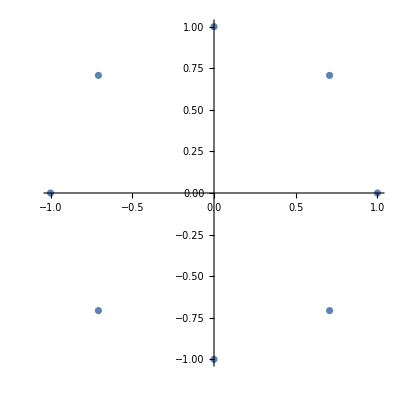

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@pts,AspectRatio->1]
```

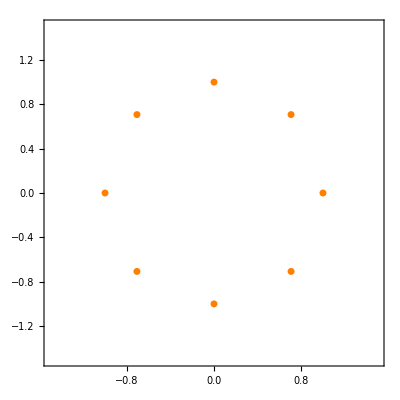

```mathematica
ComplexListPlot[pts,PlotStyle->Directive[RGBColor[1,0.5,0],AbsolutePointSize[5]],PlotRange->1.5,Frame->True]
```

```mathematica
ComplexListPlot[pts,PlotStyle->Directive[RGBColor[1,0.5,0],AbsolutePointSize[5]],PolarAxes->True,PolarGridLines->Automatic]
```

-Graphics-

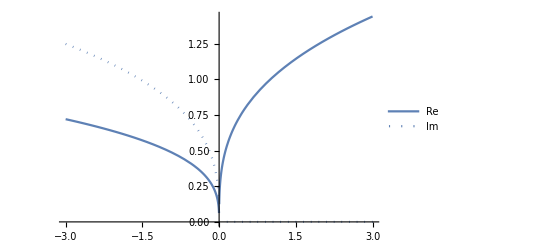

```mathematica
ReImPlot[x^(1/3),{x,-3,3},PlotLegends->Automatic]
```

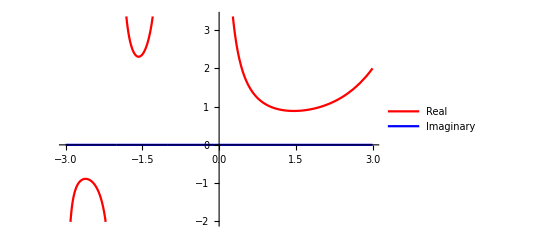

```mathematica
ReImPlot[Gamma[z],{z,-3,3},PlotLegends->Automatic,ReImStyle->{Red,Directive[Blue,Dashing[{}]]},ReImLabels->{"Real","Imaginary"}]
```

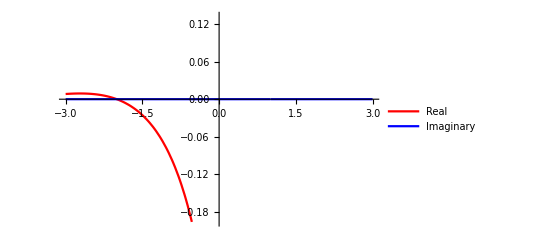

```mathematica
ReImPlot[Zeta[z],{z,-3,3},PlotLegends->Automatic,ReImStyle->{Red,Directive[Blue,Dashing[{}]]},ReImLabels->{"Real","Imaginary"}]
```

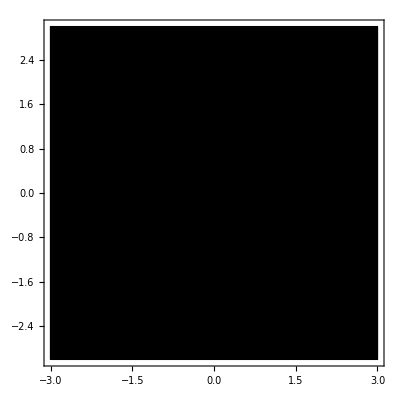

```mathematica
ComplexPlot[(z^4+3 z^2-4)/z,{z,-3-3 I,3+3 I},PlotLegends->Automatic]
```

```mathematica
ComplexPlot3D[(z^4+3 z^2-4)/z,{z,-3-3 I,3+3 I},PlotLegends->Automatic]
```

-Graphics3D-

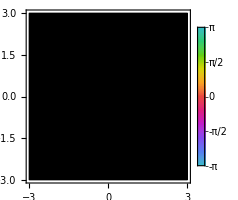

```mathematica
ComplexPlot[z,{z,-3-3 I,3+3 I},Sequence[Epilog->{Arrowheads[0.065],Thick,Arrow[Table[{Cos[t],Sin[t]},{t,-Pi,Pi,Pi/50}]]},PlotLegends->Automatic,ColorFunction->None,ImageSize->200]]
```

```mathematica
f[g[h[x]]]
```

Gamma[-ⅈ+g[h[x]]]^2/Gamma[ⅈ+g[h[x]]]^2

```mathematica
ClearAll[f]
```

```mathematica
f[g[h[x]]]
```

f[g[h[x]]]

```mathematica
∫f[g[h[x]]]ⅆx
```

∫f[g[h[x]]]ⅆx

```mathematica
D[f[g[h[x]]], x]
```

f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
∫f'[g[h[x]]] g'[h[x]] h'[x]ⅆx
```

f[g[h[x]]]

```mathematica
ClearAll[x]
```

```mathematica
f'[g[h[x]]] g'[h[x]] h'[x]==a[x] h'[x]
```

f'[g[h[x]]] g'[h[x]] h'[x]==a[x] h'[x]

```mathematica
Integrate[f'[g[h[x]]] g'[h[x]] h'[x],x]==Integrate[a[x] h'[x],x]
```

f[g[h[x]]]==∫a[x] h'[x]ⅆx

```mathematica
TraditionalForm[f[g[h[x]]]==∫a[x] h'[x]ⅆx]
```

f(g(h(x)))==∫a(x) h'(x)ⅆx

```mathematica
D[f[g[h[x]]]==∫a[x] h'[x]ⅆx,x]
```

f'[g[h[x]]] g'[h[x]] h'[x]==a[x] h'[x]

```mathematica
MultiplySides[f'[g[h[x]]] g'[h[x]] h'[x]==a[x] h'[x],1/h'[x]]
```

Piecewise[{{f'[g[h[x]]] g'[h[x]]==a[x], 1/h'[x]≠0}, {f'[g[h[x]]] g'[h[x]] h'[x]==a[x] h'[x], True}}]

```mathematica
Integrate[x x,x]
```

x^3/3

```mathematica
Integrate[f[x],x]
```

∫f[x]ⅆx

```mathematica
Integrate[f'[x],x]
```

f[x]

```mathematica
Integrate[f'[x]g'[x],x]
```

∫f'[x] g'[x]ⅆx

```mathematica
Integrate[f'[x]g[x],x]
```

∫g[x] f'[x]ⅆx

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]==Integrate[a[x]+g'[x]f[x],x]
```

f[x] g[x]==∫(a[x]+f[x] g'[x])ⅆx

```mathematica
f[x] g[x]==∫(a[x])ⅆx+∫f[x] g'[x]ⅆx
```

f[x] g[x]==∫a[x]ⅆx+∫f[x] g'[x]ⅆx

```mathematica
f[x] g[x]-∫f[x] g'[x]ⅆx==∫a[x]ⅆx
```

f[x] g[x]-∫f[x] g'[x]ⅆx==∫a[x]ⅆx

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]==Integrate[a[x]+g'[x]f[x],x]
```

```mathematica
Integrate[f'[x]g[x],x]==Integrate[a[x],x]
```

∫g[x] f'[x]ⅆx==∫a[x]ⅆx

```mathematica
Integrate[f'[x]g[x],x]+Integrate[+g'[x]f[x],x]==Integrate[a[x],x]+Integrate[+g'[x]f[x],x]
```

∫g[x] f'[x]ⅆx+∫f[x] g'[x]ⅆx==∫a[x]ⅆx+∫f[x] g'[x]ⅆx

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]==Integrate[a[x],x]+Integrate[+g'[x]f[x],x]
```

f[x] g[x]==∫a[x]ⅆx+∫f[x] g'[x]ⅆx

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]-Integrate[+g'[x]f[x],x]==Integrate[a[x],x]
```

f[x] g[x]-∫f[x] g'[x]ⅆx==∫a[x]ⅆx

```mathematica
g[x] f'[x]==a'[x]
```

g[x] f'[x]==a'[x]

```mathematica
Integrate[g[x] f'[x],x]==Integrate[a'[x],x]
```

∫g[x] f'[x]ⅆx==a[x]

```mathematica
∫g'[x] f[x]ⅆx
```

∫f[x] g'[x]ⅆx

```mathematica
∫g[x] f'[x]ⅆx+∫f[x] g'[x]ⅆx==a[x]+∫f[x] g'[x]ⅆx
```

∫g[x] f'[x]ⅆx+∫f[x] g'[x]ⅆx==a[x]+∫f[x] g'[x]ⅆx

```mathematica
∫g[x] f'[x]+f[x] g'[x]ⅆx==a[x]+∫f[x] g'[x]ⅆx
```

Integrate::nodiffd: ∫g[x]f'[x] cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
∫(g[x] f'[x]+f[x] g'[x])ⅆx==a[x]+∫f[x] g'[x]ⅆx
```

f[x] g[x]==a[x]+∫f[x] g'[x]ⅆx

```mathematica
f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]
```

f[x] g[x]-∫f[x] g'[x]ⅆx==a[x]

```mathematica
f[x] g[x]-∫f[x] g'[x]ⅆx+∫f'[x] g[x]ⅆx==a[x]+∫f'[x] g[x]ⅆx
```

f[x] g[x]+∫g[x] f'[x]ⅆx-∫f[x] g'[x]ⅆx==a[x]+∫g[x] f'[x]ⅆx

```mathematica
f[x] g[x]+∫(g[x] f'[x]-f[x] g'[x])ⅆx==a[x]+∫g[x] f'[x]ⅆx
```

f[x] g[x]+∫(g[x] f'[x]-f[x] g'[x])ⅆx==a[x]+∫g[x] f'[x]ⅆx

```mathematica
f[x] g[x]-(∫(g[x] f'[x]+f[x] g'[x])ⅆx)==a[x]-∫g[x] f'[x]ⅆx
```

0==a[x]-∫g[x] f'[x]ⅆx

```mathematica
∫g[x] f'[x]ⅆx==a[x]
```

∫g[x] f'[x]ⅆx==a[x]

```mathematica
f[x]f[x]
```

f[x]^2

```mathematica
Integrate[x,x]
```

x^2/2

```mathematica
Integrate[f'[x]g[x]+g'[x]f[x],x]
```

f[x] g[x]

```mathematica
With[{f=Function[x, x],g=Function[x,x x]},f[x] g[x]==∫(a[x])ⅆx+∫f[x] g'[x]ⅆx]
```

x^3==(2 x^3)/3+∫a[x]ⅆx

```mathematica
Solve[x^3==(2 x^3)/3+∫a[x]ⅆx,∫a[x]ⅆx]
```

{{∫a[x]ⅆx→x^3/3}}

```mathematica
Integrate[x x x,x]
```

x^4/4

```mathematica
Integrate[x x,x]
```

x^3/3

```mathematica
f[x] g[x]-∫f[x] g'[x]ⅆx==∫(a[x])ⅆx
```

f[x] g[x]-∫f[x] g'[x]ⅆx==∫a[x]ⅆx

```mathematica
D[f[x]g[x],x]
```

g[x] f'[x]+f[x] g'[x]

```mathematica
g[x] f'[x]+f[x] g'[x]==a[x]
```

g[x] f'[x]+f[x] g'[x]==a[x]

```mathematica
g[x] f'[x]+f[x] g'[x]==a'[x]
```

g[x] f'[x]+f[x] g'[x]==a'[x]

```mathematica
Integrate[g[x] f'[x]+f[x] g'[x],x]==Integrate[a'[x],x]
```

f[x] g[x]==a[x]

```mathematica
Integrate[g[x] f'[x],x]+Integrate[f[x] g'[x],x]==Integrate[a'[x],x]
```

∫g[x] f'[x]ⅆx+∫f[x] g'[x]ⅆx==a[x]

```mathematica
Integrate[g[x] f'[x],x]==Integrate[a'[x],x]-Integrate[f[x] g'[x],x]
```

∫g[x] f'[x]ⅆx==a[x]-∫f[x] g'[x]ⅆx

```mathematica
D[Integrate[g[x] f'[x],x],x]==D[Integrate[a'[x],x]-Integrate[f[x] g'[x],x],x]
```

g[x] f'[x]==a'[x]-f[x] g'[x]

```mathematica
Solve[g[x] f'[x]==a'[x]-f[x] g'[x],g[x]]
```

{{g[x]→(a'[x]-f[x] g'[x])/f'[x]}}

```mathematica
g[x]==(a'[x]-f[x] g'[x])/f'[x]
```

g[x]==(a'[x]-f[x] g'[x])/f'[x]

```mathematica
Integrate[f[x],{x,a,b}]
```

∫_a^b f[x]ⅆx

```mathematica
Integrate[f'[x],{x,a,b}]
```

∫_a^b f'[x]ⅆx

```mathematica
∫(∫_a^b f'[x]ⅆx)ⅆa
```

∫(∫_a^b f'[x]ⅆx)ⅆa

```mathematica
∂_a ∫(∫_a^b f'[x]ⅆx)ⅆa
```

∫_a^b f'[x]ⅆx

```mathematica
Integrate[x^2,{x,-2,2}]
```

16/3

```mathematica
Integrate[D[x^2,x],{x,-2,2}]
```

0

```mathematica
FullSimplify[Integrate[D[x^2,x],{x,-a,a}],a∈Reals]
```

0

```mathematica
FullSimplify[Integrate[D[x^2,x],{x,-a,a}],a∈]
```

0

```mathematica
FullSimplify[Integrate[D[x^2,x],{x,0,a}],a∈]
```

a^2

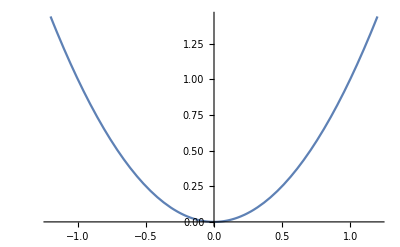

```mathematica
Plot[a^2,{a,-1.2,1.2}]
```

```mathematica
Integrate[1/(1+x^2),x]
```

ArcTan[x]

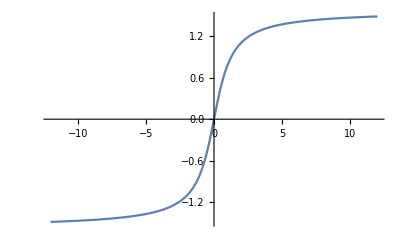

```mathematica
Plot[ArcTan[x],{x,-12.,12.}]
```

```mathematica
Limit[Integrate[1/(1+x^2),{x,0,a}],a->∞]
```

π/2

```mathematica
NIntegrate[1/(1+x^2),{x,0,a}]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

NIntegrate[1/(1+x^2),{x,0,a}]

```mathematica
NIntegrate[1/(1+x^2),{x,0,∞}]
```

1.5708

```mathematica
1.570796326794894/π
```

0.5

```mathematica
π/2
```

π/2

```mathematica
{x,f[x]}-{x,0}
```

{0,f[x]}

```mathematica
Norm[{x,f[x]}-{x,0}]
```

Abs[f[x]]

```mathematica
FullSimplify[Norm[{x,f[x]}-{x,0}],{x,f[x]}∈Reals]
```

Abs[f[x]]

```mathematica
With[{f=Identity},Abs[f[x]]]
```

Abs[x]

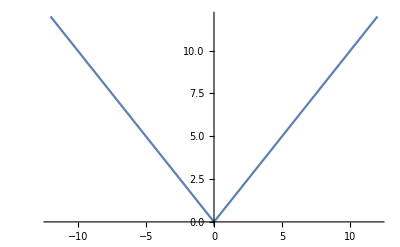

```mathematica
Plot[Abs[x],{x,-12.,12.}]
```

```mathematica
Integrate[Abs[x],{x,0,1}]
```

1/2

```mathematica
Integrate[x,{x,0,1}]
```

1/2

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
Norm[{Cos[t],Sin[t]}-{t,t}]
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
FullSimplify[Norm[{Cos[t],Sin[t]}-{t,t}],t∈Reals]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
FullSimplify[Norm[{Cos[t],Sin[t]}-{t,t}],t∈]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

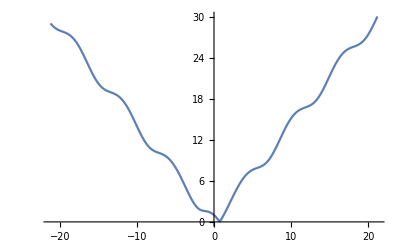

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,-21.205750411731103,21.205750411731103}]
```

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

∫_0^(2 π) √(1+2 t^2-2 t (Cos[t]+Sin[t]))ⅆt

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2 π}]
```

28.9736

```mathematica
28.973554590759658/π
```

9.22257

```mathematica
28.973554590759658/π^2
```

2.93563

```mathematica
28.973554590759658/π^3
```

0.934442

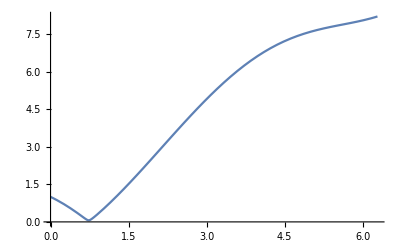

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

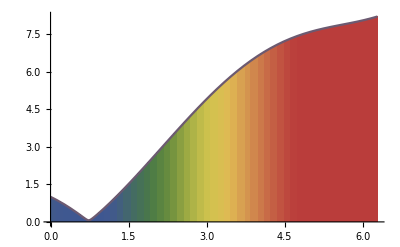

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π},ColorFunction->"DarkRainbow",Filling->Axis]
```

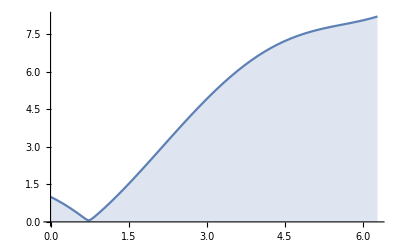

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π},Filling->Axis]
```

```mathematica
√(1+2 t^2-2 t (Cos[t]+Sin[t]))==a'[x]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))==a'[x]

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t]))==a'[x],x]
```

∫(√(1+2 t^2-2 t (Cos[t]+Sin[t]))==a'[x])ⅆx

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),x]==Integrate[a'[x],x]
```

x √(1+2 t^2-2 t (Cos[t]+Sin[t]))==a[x]

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),x]
```

x √(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),t]==Integrate[a'[t],t]
```

∫√(1+2 t^2-2 t (Cos[t]+Sin[t]))ⅆt==a[t]

```mathematica
(√(1+2 t^2-2 t (Cos[t]+Sin[t])))^2==a'[t]^2
```

1+2 t^2-2 t (Cos[t]+Sin[t])==a'[t]^2

```mathematica
DSolve[1+2 t^2-2 t (Cos[t]+Sin[t])==a'[t]^2,{a[t]},{t}]
```

{{a[t]→C[1]+-√(1-2 Cos[K[1]] K[1]+2 K[1]^2-2 K[1] Sin[K[1]])K[1]1t},{a[t]→C[1]+√(1-2 Cos[K[2]] K[2]+2 K[2]^2-2 K[2] Sin[K[2]])K[2]1t}}

```mathematica
Integrate[1+2 t^2-2 t (Cos[t]+Sin[t]),t]==Integrate[a'[t]^2,t]
```

t+(2 t^3)/3-2 Cos[t]+2 t Cos[t]-2 Sin[t]-2 t Sin[t]==∫a'[t]^2 ⅆt

```mathematica
Dt[f[x]g[x]]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
DiracDelta[3]
```

0

```mathematica
DiracDelta[0]
```

DiracDelta[0]

```mathematica
DiracDelta[1]
```

0

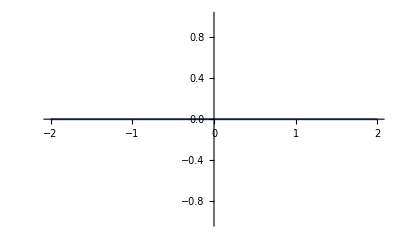

```mathematica
Plot[DiracDelta[x],{x,-2,2}]
```

```mathematica
Integrate[1+2 t^2-2 t (Cos[t]+Sin[t]),x]==Integrate[a'[t]^2,t]
```

x+2 t^2 x-2 t x (Cos[t]+Sin[t])==∫a'[t]^2 ⅆt

```mathematica
Integrate[1+2 t^2-2 t (Cos[t]+Sin[t]),t]==Integrate[a'[t]^2,t]
```

t+(2 t^3)/3-2 Cos[t]+2 t Cos[t]-2 Sin[t]-2 t Sin[t]==∫a'[t]^2 ⅆt

```mathematica
Limit[Integrate[Sin[x]/x,{x,0,a}],a->∞]
```

π/2

```mathematica
Sin[x]/x
```

Sin[x]/x

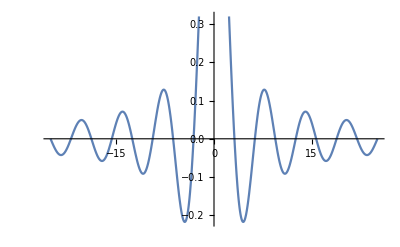

```mathematica
Plot[Sin[x]/x,{x,-25.132741228718345,25.132741228718345}]
```

```mathematica
Integrate[Sin[x]/x,{x,0,5}]
```

SinIntegral[5]

```mathematica
SinIntegral[x]
```

SinIntegral[x]

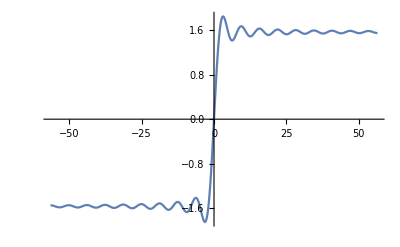

```mathematica
Plot[SinIntegral[x],{x,-56.548667764616276,56.548667764616276}]
```

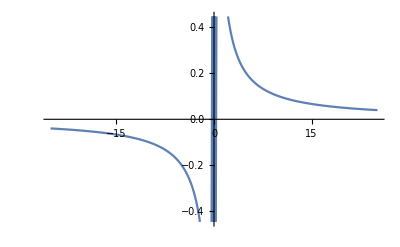

```mathematica
Plot[Sin[1/x],{x,-25.132741228718345,25.132741228718345}]
```

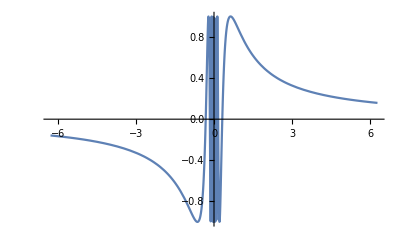

```mathematica
Plot[Sin[1/x],{x,-2π,2π}]
```

```mathematica
Integrate[Sin[1/x],{x,0,2π}]
```

-CosIntegral[1/(2 π)]+2 π Sin[1/(2 π)]

```mathematica
Integrate[Sin[1/x],{x,0,a}]
```

√(1/a^2) (-√(a^2) CosIntegral[1/(√(a^2))]+a^2 Sin[1/(√(a^2))])

```mathematica
FullSimplify[Integrate[Sin[1/x],{x,0,a}],a∈]
```

-CosIntegral[1/a]+a Sin[1/a]

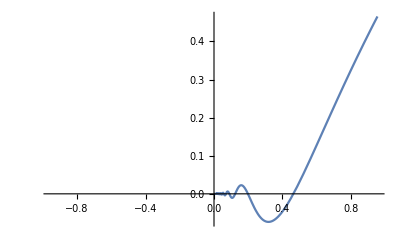

```mathematica
Plot[-CosIntegral[1/a]+a Sin[1/a],{a,-0.9549296585513721,0.9549296585513721}]
```

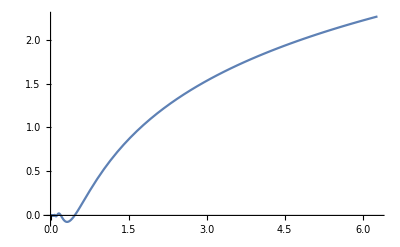

```mathematica
Plot[-CosIntegral[1/a]+a Sin[1/a],{a,0,2π}]
```

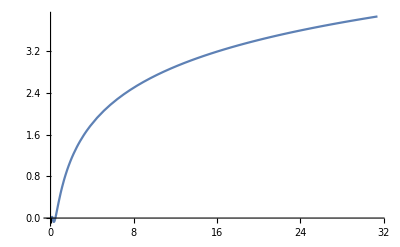

```mathematica
Plot[-CosIntegral[1/a]+a Sin[1/a],{a,0,10π}]
```

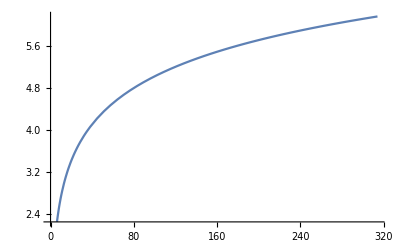

```mathematica
Plot[-CosIntegral[1/a]+a Sin[1/a],{a,0,100π}]
```

```mathematica
Exp[-CosIntegral[1/a]+a Sin[1/a]]
```

ⅇ^(-CosIntegral[1/a]+a Sin[1/a])

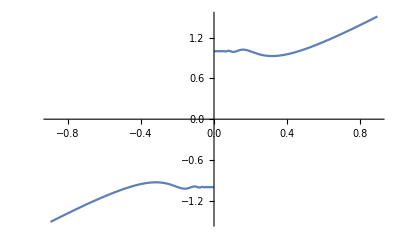

```mathematica
Plot[ⅇ^(-CosIntegral[1/a]+a Sin[1/a]),{a,-0.8952465548919113,0.8952465548919113}]
```

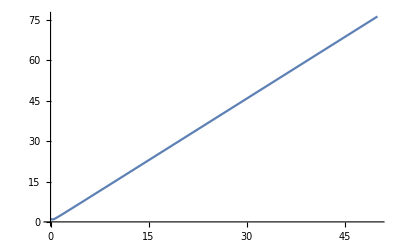

```mathematica
Plot[ⅇ^(-CosIntegral[1/a]+a Sin[1/a]),{a,0,50}]
```

```mathematica
y
```

y

```mathematica
ClearAll[y]
```

```mathematica
({x''[t],y''[t]}.{-y'[x],x'[t]})/Norm[{x'[t],y'[t]}]^3
```

(-y'[x] x''[t]+x'[t] y''[t])/((Abs[x'[t]]^2+Abs[y'[t]]^2)^(3/2))

```mathematica
FullSimplify[({x''[t],y''[t]}.{-y'[x],x'[t]})/Norm[{x'[t],y'[t]}]^3,{t,x'[t],y'[t],x''[t],y''[t]}∈Reals]
```

(-y'[x] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))

```mathematica
With[{x=Identity},(-y'[x] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))]
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
With[{y=Function[a,ⅇ^(-CosIntegral[1/a]+a Sin[1/a])]},y''[t]/((1+y'[t]^2)^(3/2))]
```

(ⅇ^(-CosIntegral[1/t]+t Sin[1/t]) Sin[1/t]^2+ⅇ^(-CosIntegral[1/t]+t Sin[1/t]) (-(2 Cos[1/t])/t^2-Sin[1/t]/t^3-(-t^2 Cos[1/t]-t Sin[1/t])/t^4))/((1+ⅇ^(-2 CosIntegral[1/t]+2 t Sin[1/t]) Sin[1/t]^2)^(3/2))

```mathematica
FullSimplify[With[{y=Function[a,ⅇ^(-CosIntegral[1/a]+a Sin[1/a])]},y''[t]/((1+y'[t]^2)^(3/2))],{t,y'[t],y''[t]}∈Reals]
```

(ⅇ^(CosIntegral[1/t]+t Sin[1/t]) (-Cos[1/t]+t^2 Sin[1/t]^2))/(t^2 (ⅇ^(2 CosIntegral[1/t])+ⅇ^(2 t Sin[1/t]) Sin[1/t]^2) √(1+ⅇ^(-2 CosIntegral[1/t]+2 t Sin[1/t]) Sin[1/t]^2))

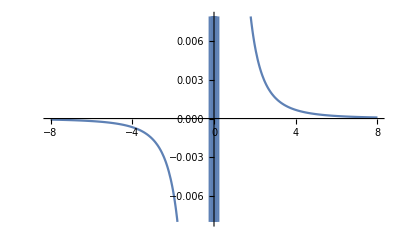

```mathematica
Plot[(ⅇ^(CosIntegral[1/t]+t Sin[1/t]) (-Cos[1/t]+t^2 Sin[1/t]^2))/(t^2 (ⅇ^(2 CosIntegral[1/t])+ⅇ^(2 t Sin[1/t]) Sin[1/t]^2) √(1+ⅇ^(-2 CosIntegral[1/t]+2 t Sin[1/t]) Sin[1/t]^2)),{t,-8,8}]
```

```mathematica
With[{y=Identity},y''[t]/((1+y'[t]^2)^(3/2))]
```

0

```mathematica
2
```

2

```mathematica
1
```

1

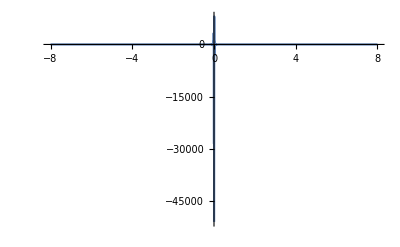

```mathematica
Plot[(ⅇ^(CosIntegral[1/t]+t Sin[1/t]) (-Cos[1/t]+t^2 Sin[1/t]^2))/(t^2 (ⅇ^(2 CosIntegral[1/t])+ⅇ^(2 t Sin[1/t]) Sin[1/t]^2) √(1+ⅇ^(-2 CosIntegral[1/t]+2 t Sin[1/t]) Sin[1/t]^2)),{t,-8,8},PlotRange->Full]
```

```mathematica
{a,b}->{a b,b-1}
```

{a,b}→{a b,-1+b}

```mathematica
f[{a_,b_}]:={a b,b-1}
```

```mathematica
f[{a_Reals,b_Reals}]:={a b,b-1}
```

```mathematica
f[{2,3}]
```

{6,2}

```mathematica
f[{a,b}]
```

{a b,-1+b}

```mathematica
f[{{},{1}}]
```

Thread::tdlen: Objects of unequal length in {} {1} cannot be combined.

{{} {1},{0}}

```mathematica
f[{1,2}]
```

{2,1}

```mathematica
f[{2,3}]
```

{6,2}

```mathematica
f[{{2,3},{4,5}}]
```

{{8,15},{3,4}}

```mathematica
SetAttributes[f,Listable]
```

```mathematica
f[{{2,3},{4,5}}]
```

{{f[2],f[3]},{f[4],f[5]}}

```mathematica
ClearAll[f]
```

```mathematica
f[{4,5}]
```

f[{4,5}]

```mathematica
f[{a_Reals,b_Reals}]:={a b,b-1}
```

```mathematica
f[{4,5}]
```

f[{4,5}]

```mathematica
f[{a_Real,b_Real}]:={a b,b-1}
```

```mathematica
f[{4,5}]
```

f[{4,5}]

```mathematica
ClearAll[f]
```

```mathematica
f[{a_Real,b_Real}]:={a b,b-1}
```

```mathematica
f[{4,5}]
```

f[{4,5}]

```mathematica
ClearAll[f]
```

```mathematica
f[{a_,b_}]:={a b,b-1}
```

```mathematica
f[{4,5}]
```

{20,4}

```mathematica
NestList[f,{4,5},5]
```

{{4,5},{20,4},{80,3},{240,2},{480,1},{480,0}}

```mathematica
NestList[f,{a,b},5]
```

{{a,b},{a b,-1+b},{a (-1+b) b,-2+b},{a (-2+b) (-1+b) b,-3+b},{a (-3+b) (-2+b) (-1+b) b,-4+b},{a (-4+b) (-3+b) (-2+b) (-1+b) b,-5+b}}

```mathematica
Grid@NestList[f,{a,b},5]
```

a | b
a b | -1+b
a (-1+b) b | -2+b
a (-2+b) (-1+b) b | -3+b
a (-3+b) (-2+b) (-1+b) b | -4+b
a (-4+b) (-3+b) (-2+b) (-1+b) b | -5+b

```mathematica
With[{c=5},Prepend[NestList[f,{a,b},c],Range@c]]
```

{{1,2,3,4,5},{a,b},{a b,-1+b},{a (-1+b) b,-2+b},{a (-2+b) (-1+b) b,-3+b},{a (-3+b) (-2+b) (-1+b) b,-4+b},{a (-4+b) (-3+b) (-2+b) (-1+b) b,-5+b}}

```mathematica
With[{c=5},Grid@Prepend[NestList[f,{a,b},c],Range@c]]
```

1 | 2 | 3 | 4 | 5
a | b |  |  | 
a b | -1+b |  |  | 
a (-1+b) b | -2+b |  |  | 
a (-2+b) (-1+b) b | -3+b |  |  | 
a (-3+b) (-2+b) (-1+b) b | -4+b |  |  | 
a (-4+b) (-3+b) (-2+b) (-1+b) b | -5+b |  |  |

```mathematica
Grid@NestList[f,{a,b},5]
```

a | b
a b | -1+b
a (-1+b) b | -2+b
a (-2+b) (-1+b) b | -3+b
a (-3+b) (-2+b) (-1+b) b | -4+b
a (-4+b) (-3+b) (-2+b) (-1+b) b | -5+b

```mathematica
f[{a_Reals,b_Reals}]:={a b,b-1}
```

```mathematica
ClearAll[f]
```

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Limit[Series[Exp[x],{x,0,a}],a->∞]
```

Series::serlim: Series order specification a is not a machine-sized integer.

lim_(a→∞) Series[ⅇ^x,{x,0,a}]

```mathematica
Series[Exp[x],{x,0,∞}]
```

Series::serlim: Series order specification ∞ is not a machine-sized integer.

Series[ⅇ^x,{x,0,∞}]

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Normal[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

```mathematica
O[x]
```

O[x]^1

```mathematica
∫∫ⅆA
```

Integrate::intnest: The integral ∫∫ⅆA cannot be interpreted. The number of definite and indefinite integral operators must match the number of differential operators.

```mathematica
Dt[A==x y]
```

Dt[A]==y Dt[x]+x Dt[y]

```mathematica
TraditionalForm[Dt[A]==y Dt[x]+x Dt[y]]
```

ⅆA==y ⅆx+x ⅆy

```mathematica
Series[Exp[x],{x,0,1}]
```

1+x+O[x]^2

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
D[Series[Exp[x],{x,0,10}],x]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+O[x]^10

```mathematica
Sum[x^i/Factorial[i],{i,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

```mathematica
Series[Exp[x],{x,0,10}]==D[Series[Exp[x],{x,0,10}],x]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11==1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+O[x]^10

```mathematica
Dt[S=x y z]
```

y z Dt[x]+x z Dt[y]+x y Dt[z]

```mathematica
TraditionalForm[y z Dt[x]+x z Dt[y]+x y Dt[z]]
```

y z ⅆx+x z ⅆy+x y ⅆz

```mathematica
ClearAll[S]
```

```mathematica
Dt[S==x y z]
```

Dt[S]==y z Dt[x]+x z Dt[y]+x y Dt[z]

```mathematica
TraditionalForm[Dt[S]==y z Dt[x]+x z Dt[y]+x y Dt[z]]
```

ⅆS==y z ⅆx+x z ⅆy+x y ⅆz

```mathematica
Cross[{a,b,c},{d,e,f}]
```

{-c e+b f,c d-a f,-b d+a e}

```mathematica
Cross[{Sin[t],0,0},{Cos[t],0,0}]
```

{0,0,0}

```mathematica
Cross[{Cos[t],0,0},{0,Sin[t],0}]
```

{0,0,Cos[t] Sin[t]}

```mathematica
{0,0,Cos[t] Sin[t]}.{0,Sin[t],0}
```

0

```mathematica
{0,0,Cos[t] Sin[t]}.{Cos[t],0,0}
```

0

```mathematica
{0,0,Cos[t] Sin[t]}.{Cos[t],0,0}×{0,Sin[t],0}
```

Cos[t]^2 Sin[t]^2

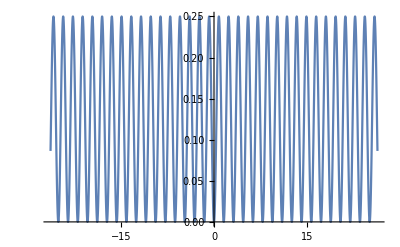

```mathematica
Plot[Cos[t]^2 Sin[t]^2,{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
Cos[t] Sin[t]
```

Cos[t] Sin[t]

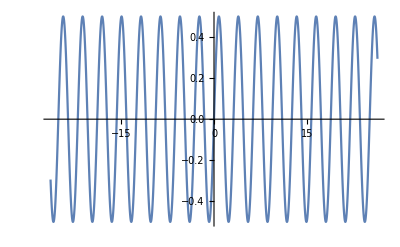

```mathematica
Plot[Cos[t] Sin[t],{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
Sum[x^i/Factorial[i],{i,0,n}]
```

(ⅇ^x Gamma[1+n,x])/(n!)

```mathematica
Sum[x^i/Factorial[i],{i,0,n}]->Sum[(i x^(i-1))/Factorial[i],{i,0,n}]
```

(ⅇ^x Gamma[1+n,x])/(n!)→((ⅇ^x (Gamma[n]+Gamma[1+n]) Gamma[1+n,x])/(Gamma[n] Gamma[1+n])+(-x^(2+n)+ⅇ^x (-1-n+x) Gamma[2+n,x])/Gamma[2+n])/x

```mathematica
Sum[x^i/Factorial[i],{i,0,n}]->Sum[(i x^(i-1))/Factorial[i],{i,0,n}]->Sum[(i(i-1) x^(i-2))/Factorial[i],{i,0,n}]
```

(ⅇ^x Gamma[1+n,x])/(n!)→((ⅇ^x (Gamma[n]+Gamma[1+n]) Gamma[1+n,x])/(Gamma[n] Gamma[1+n])+(-x^(2+n)+ⅇ^x (-1-n+x) Gamma[2+n,x])/Gamma[2+n])/x→1/x^2(ⅇ^x (1+n^2-2 n (-1+x)-x+x^2)+(ⅇ^x (1+n) Gamma[1+n,x])/Gamma[n]-((1+2 n) (x^(2+n)-ⅇ^x (-1-n+x) Gamma[2+n,x]))/Gamma[2+n]-1/((2+n)!)(2 x^(2+n)+n x^(2+n)-n x^(3+n)+x^(4+n)+ⅇ^x (2+n) (-1-n+x) Gamma[2+n]+ⅇ^x (2+3 n+n^2-2 x-2 n x+x^2) Gamma[3+n]+2 ⅇ^x Gamma[2+n,x]+3 ⅇ^x n Gamma[2+n,x]+ⅇ^x n^2 Gamma[2+n,x]-2 ⅇ^x x Gamma[2+n,x]-ⅇ^x n x Gamma[2+n,x]-2 ⅇ^x Gamma[3+n,x]-3 ⅇ^x n Gamma[3+n,x]-ⅇ^x n^2 Gamma[3+n,x]+2 ⅇ^x x Gamma[3+n,x]+2 ⅇ^x n x Gamma[3+n,x]-ⅇ^x x^2 Gamma[3+n,x]))

```mathematica
Norm[Cos[t]]Norm[Sin[t]]Norm[t]Sin[θ]
```

Norm[t] Norm[Cos[t]] Norm[Sin[t]] Sin[θ]

```mathematica
Integrate[Integrate[(1-a)x+a x^2,{a,0,1}],{x,0,1}]
```

5/12

```mathematica
Manipulate[
Plot[(1-a)x+a x^2,{x,0,1}]
,{a,0,1}]
```

```mathematica
Integrate[x x-x,{x,0,1}]
```

-1/6

```mathematica
Laplacian[f[x,y],{x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
D[f[x,y], x]+D[f[x,y], y]
```

f^(0,1)[x,y]+f^(1,0)[x,y]

```mathematica
√(Derivative[0,1][f][x,y]+Derivative[1,0][f][x,y])
```

√(f^(0,1)[x,y]+f^(1,0)[x,y])

```mathematica
f[x,y] √(Derivative[0,1][f][x,y]+Derivative[1,0][f][x,y])
```

f[x,y] √(f^(0,1)[x,y]+f^(1,0)[x,y])

```mathematica
With[{f=Function[{x,y},√(1-x^2-y^2)]},f[x,y] √(Derivative[0,1][f][x,y]+Derivative[1,0][f][x,y])]
```

√(1-x^2-y^2) √(-x/(√(1-x^2-y^2))-y/(√(1-x^2-y^2)))

```mathematica
Integrate[√(1-x^2-y^2) √(-x/(√(1-x^2-y^2))-y/(√(1-x^2-y^2))),{x,-1,1},{y,-1,1}]
```

$Aborted

```mathematica
NIntegrate[√(1-x^2-y^2) √(-x/(√(1-x^2-y^2))-y/(√(1-x^2-y^2))),{x,-1,1},{y,-1,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.880584+1.22625 ⅈ and 0.000249511 for the integral and error estimates.

0.880584+1.22625 ⅈ

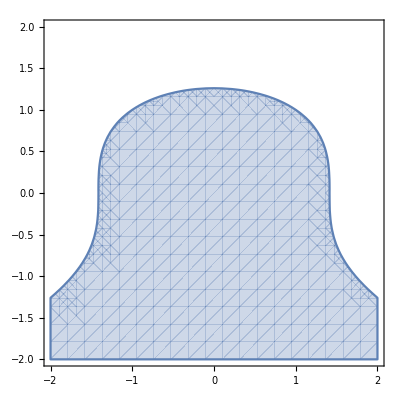

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2}]
```

```mathematica
RegionPlot[x^2+y^3==2,{x,-2,2},{y,-2,2}]
```

-Graphics-

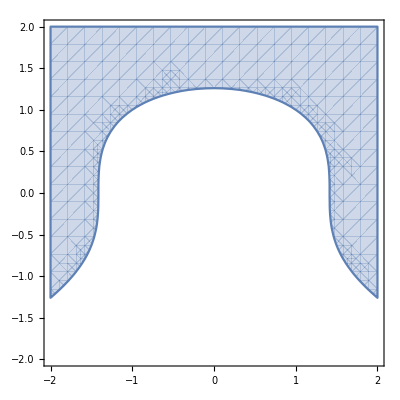

```mathematica
RegionPlot[x^2+y^3>2,{x,-2,2},{y,-2,2}]
```

```mathematica
RegionPlot[x^2+y^3≥2,{x,-2,2},{y,-2,2}]
```

-Graphics-

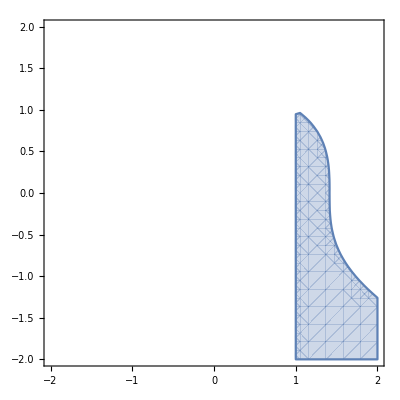

```mathematica
RegionPlot[x^2+y^3≤2∧x>1,{x,-2,2},{y,-2,2}]
```

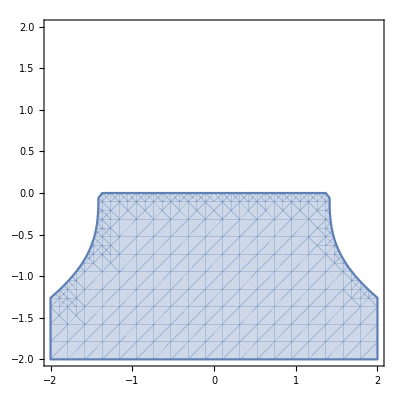

```mathematica
RegionPlot[x^2+y^3≤2∧x^2+y^3<x^2,{x,-2,2},{y,-2,2}]
```

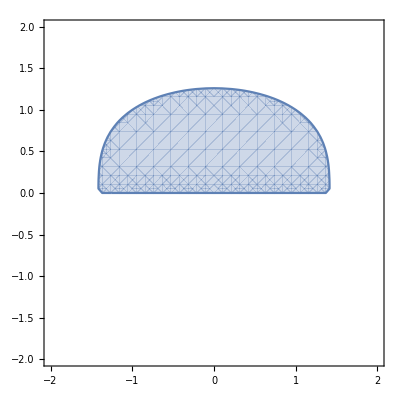

```mathematica
RegionPlot[x^2+y^3≤2∧x^2+y^3>x^2,{x,-2,2},{y,-2,2}]
```